```mathematica
(* set your home directory *)
SetDirectory[NotebookDirectory[]<>"tests/"];
(* numb of meshes *)
max=Import["numbOfRows.dat","List"][[1]]
```

5

# Model problems

## Pure (D, N, or R) problem on curcular domain

### Error analysis

```mathematica
Do[
path=ToString[i]<>"/";
Subscript[Δh, i]=Import[path<>"deltaH.dat","List"][[1]];
Subscript[ξ, i]=Import[path<>"xi.dat","List"];
Subscript[u, i]=Import[path<>"u.dat","List"];
Subscript[Δ, i]=Norm[Subscript[ξ, i]-Subscript[u, i]];
Subscript[δ, i]=Norm[Subscript[ξ, i]-Subscript[u, i]]/(Norm@Subscript[u, i]);
If[i>1,Subscript[k, i]=Subscript[δ, i-1]/Subscript[δ, i]];
Subscript[nodes, i]=Import[path<>"nodes.dat","Table"];
triangles=Import[path<>"triangles.dat","Table"]+1;
Subscript[𝒦, i]=MeshRegion[Subscript[nodes, i],Triangle/@triangles],
{i,max}]
Subscript[k, 1]="";
```

```mathematica
header=Style[#,Bold,Larger]&/@{"n","Δh","Δ_h","δ_h","(δ_(2  h))/δ_h"};
data=Table[{MeshCellCount[Subscript[𝒦, i],0],ScientificForm[Subscript[Δh, i],3],ScientificForm[Subscript[Δ, i],3],ScientificForm[Subscript[δ, i],3],NumberForm[Subscript[k, i],3]},{i,max}];
table=Grid[PrependTo[data,header],Frame->All,Spacings-> {1,1}]
```

n | Δh | Δ_h | δ_h | (δ_(2  h))/δ_h
13 | 7.65×10^-1 | 1.05×10^-1 | 1.68×10^-2 | 
41 | 4.2×10^-1 | 4.79×10^-2 | 4.6×10^-3 | 3.64
145 | 2.22×10^-1 | 2.23×10^-2 | 1.19×10^-3 | 3.86
545 | 1.14×10^-1 | 1.05×10^-2 | 2.95×10^-4 | 4.04
2113 | 5.75×10^-2 | 4.99×10^-3 | 7.25×10^-5 | 4.07

### Domain

Coarse mesh: h

Numb of nodes: 13

Numb of elements: 16

Nodes’ numeration

-Graphics-

Elements’ numeration

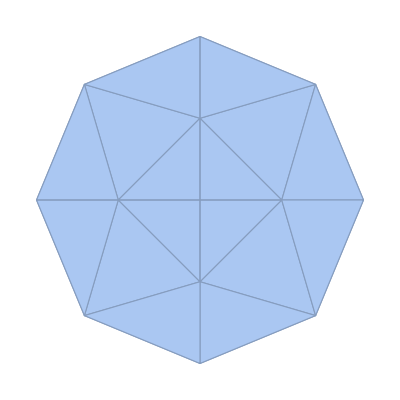

Fine mesh: h / 2

Numb of nodes: 41

Numb of elements: 64

-Graphics-

Fine mesh: h / 3

Numb of nodes: 145

Numb of elements: 256

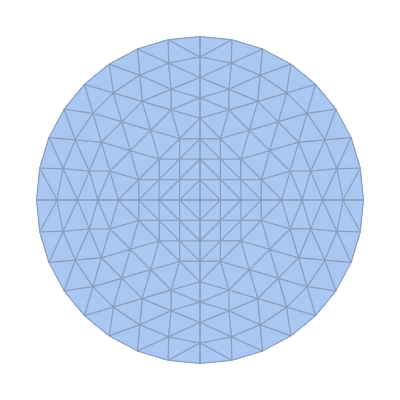

Fine mesh: h / 4

Numb of nodes: 545

Numb of elements: 1024

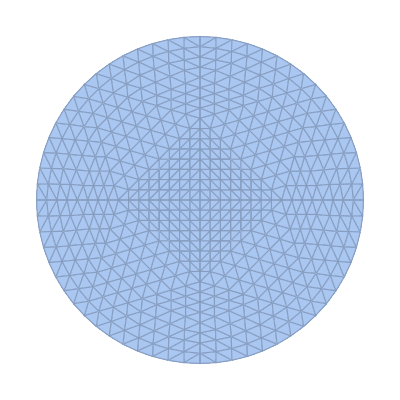

Fine mesh: h / 5

Numb of nodes: 2113

Numb of elements: 4096

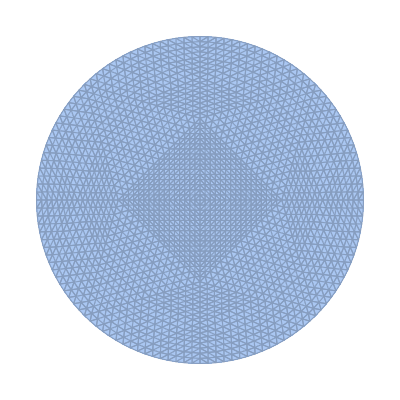

```mathematica
Do[
If[i==1,
Print@Style["Coarse mesh: h","Subsection"],
Print@Style[StringReplace["Fine mesh: h / size","size"-> ToString@i],"Subsection"]
];
Print["Numb of nodes: "<>ToString@MeshCellCount[Subscript[𝒦, i],0]];
Print["Numb of elements: "<>ToString@MeshCellCount[Subscript[𝒦, i],2]];
If[i==1,
Print@Style["Nodes’ numeration",Larger,Bold];
Print@HighlightMesh[Subscript[𝒦, i],0,MeshCellLabel->{0->"Index"}];
Print@Style["Elements’ numeration",Larger,Bold];
Print@HighlightMesh[Subscript[𝒦, i],3,MeshCellLabel->{2->"Index"}],
If[i≥ 3,
Print@Subscript[𝒦, i],
Print@HighlightMesh[Subscript[𝒦, i],0,MeshCellLabel->{0->"Index"}]
]
],
{i,max}]
```

### Plotting

```mathematica
Do[
Subscript[u, h]=Interpolation[Table[{Subscript[nodes, i][[j]],Subscript[ξ, i][[j]]},{j,Length@Subscript[ξ, i]}],InterpolationOrder->1];
Print@Plot3D[Subscript[u, h][x,y],{x,y}∈Subscript[𝒦, i],PlotLabel->StringReplace["FEM soln, u_(h / size)(x,y)","size"-> ToString@i],AxesLabel->Automatic],
{i,max}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»